```mathematica
poly[x_]:=-x^2+30x
intPoly[x_]=Integrate[poly[x],x];
polyPoints = Table[{i,poly[i]},{i,0,50}];
integralPoints = Table[{i,intPoly[i]},{i,0,50}];
```

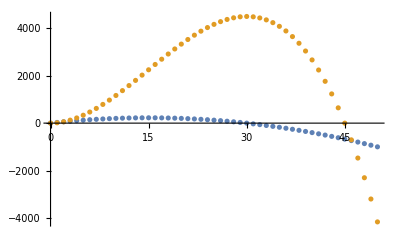

```mathematica
ListPlot@{polyPoints,integralPoints}
```

```mathematica
poly[x_]:=x^2+2x
intPoly[x_]=Integrate[poly[x],x]
integralPoints = Table[{i,intPoly[i]},{i,0,50}]
```

x^2+x^3/3

{{0,0},{1,4/3},{2,20/3},{3,18},{4,112/3},{5,200/3},{6,108},{7,490/3},{8,704/3},{9,324},{10,1300/3},{11,1694/3},{12,720},{13,2704/3},{14,3332/3},{15,1350},{16,4864/3},{17,5780/3},{18,2268},{19,7942/3},{20,9200/3},{21,3528},{22,12100/3},{23,13754/3},{24,5184},{25,17500/3},{26,19604/3},{27,7290},{28,24304/3},{29,26912/3},{30,9900},{31,32674/3},{32,35840/3},{33,13068},{34,42772/3},{35,46550/3},{36,16848},{37,54760/3},{38,59204/3},{39,21294},{40,68800/3},{41,73964/3},{42,26460},{43,85054/3},{44,90992/3},{45,32400},{46,103684/3},{47,110450/3},{48,39168},{49,124852/3},{50,132500/3}}

```mathematica
poly[x_]:=-x^2+30x
intPoly[x_]=Integrate[poly[x],x];
polyPoints = Table[{i,poly[i]},{i,0,50}];
integralPoints = Table[{i,intPoly[i]},{i,0,50}];
ListPlot@{polyPoints,integralPoints}
```

-Graphics-

```mathematica
`
```

```mathematica
Table[]
```

```mathematica
list ={};
sizeOfList=Null;
polynomials={}
ogPolynomial[x_]:=1/2-[x-1/2]
generateFunction[polynomials_,current_]:=
Module[
{
sourceAlpha=source,
currentAlpha=current,
iterator=1
},
{
While[
iterator<Length[source]+1, 

(*Print[iterator, Length[source]];*)
AppendTo[currentAlpha,source[[iterator]]];
Recurse[listRemove[sourceAlpha,iterator],currentAlpha];
currentAlpha = current;
iterator++

];

If[Length[currentAlpha]==sizeOfList,
AppendTo[list,currentAlpha];
];
}
];
```

```mathematica
Bernstein
```

```mathematica
Plot[Evaluate[Table[BernsteinBasis[3,k,x],{k,0,3}]],{x,0,1}]
```

```mathematica
Table[BernsteinBasis[3,k,"x"],{k,0,3}]
```

{BernsteinBasis[3,0,x],BernsteinBasis[3,1,x],BernsteinBasis[3,2,x],BernsteinBasis[3,3,x]}

```mathematica
BernsteinBasis[3,2,ExpressionCell["x"]]
```

BernsteinBasis[3,2,x]

```mathematica
Bern
```